# A block climbing a circle and cycloid:

## Energy dissipated due to friction

We will parameterize the cycloid and the circle by





we  need the y-coordinate to coincide at the same height, which will occur at different tangential angles :

```mathematica
Manipulate[ParametricPlot[{A{Sin[ϕ],(1-Cos[ϕ])},B{2ϕ+Sin[2ϕ],1-Cos[2ϕ]},{C ϕ,-C + C Cosh[ϕ]},{ Tan[ϕ]/2,(Tan[ϕ]/2)^2}},{ϕ,0,1.2Pi/2},PlotLegends->{"Circle","Cycloid","Catenary"},PlotRange->{{0,1.7},{0,1.5}}],{A,1.3,2},{B,0.37,1},{C,1.016797,2},{P,1,2}]
```

## Intersection

In order to make the circle intersect the cycloid, parameterized as
 


In particular, I will focus on the case that the particle gets to the cusp of the cycloid and design a circle that intersects the cusp. Since the cusp is defined by


and if we want the circle to cross that point, we need


which leads to 


where H is a fixed height I have chosen. This leads to the system of equations




From these equations, we obtain




In the case of the catenary,

we need

thus




Then we need to solve



We will solve these equations in the following section.

### Solution

In principle, one has to find the intersection between the two curves:
π/2(1-Cos[ϕcyc])=Sin[ϕcyc]

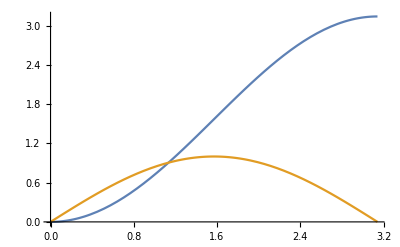

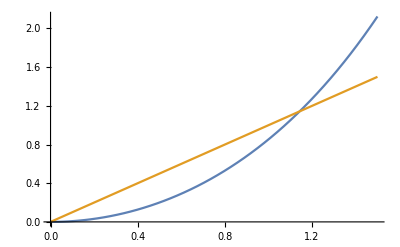

```mathematica
Plot[{π/2(1-Cos[p]),Sin[p]},{p,0,Pi}]
Plot[{π/2(Cosh[u]-1),u},{u,0,1.5}]
```

So it looks like the solution is around ϕcyc~1.3 or so, for the circle.

Replacing Cos[p]=√(1-Sin[p]^2) and x=Sin[p], we have an algebraic equation
1-√(1-x^2)=2 x/π

which is actually very easy to solve and the solution is:

Sin[ϕcyc]= (4π)/(4+π^2) ==> ϕcyc~ 1.133823 radian ~ 72% (π/2)   

This implies that
A=(πH/2)/((4π)/(4+π^2)) =(πH/2)/ Sin[ϕcyc]
B=H/2

```mathematica
ArcSin[4 Pi/(4 + Pi^2)]
```

ArcSin[(4 π)/(4+π^2)]

```mathematica
N[ArcSin[4 Pi/(4 + Pi^2)]]
```

1.13382

```mathematica
1-Cos[ArcSin[4 Pi/(4 + Pi^2)]]
```

1-√(1-(16 π^2)/((4+π^2)^2))

At this parametric value, the circle is at 
r_circle(ϕcyc) =  A(Sin[ϕcyc], (1-Cos[ϕcyc]) ) = A((4π)/(4+π^2),1-√(1-(16 π^2)/((4+π^2)^2)))=(πH/2,H)=((πB,2B))

Verifying the y coordinte equals H =  A (1-Cos[ϕcyc]):

```mathematica
N[H(π/2)/((4π)/(4+π^2))(1-√(1-(16 π^2)/((4+π^2)^2)))]
```

1. H

In terms of a fraction of π/2, this angle is

```mathematica
ϕcyc=ArcSin[(4 π)/(4+π^2)];
N[ϕcyc/(π/2)]
```

0.721814

so it is basically between (π/4) and (π/2).

### Numerical Solution for the catenary

```mathematica
Solve[π/2(Cosh[u]-1)==u,u]
ucyc=FindRoot[π/2(Cosh[u]-1)-u,{u,1}]
ucyc = u/.ucyc
Sinh[ucyc]
ϕcyccat = ArcTan[Sinh[ucyc]]

Print["Solution ϕcyccat/(π/2):"]
ϕcyccat/(π/2)
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[1/2 π (-1+Cosh[u])==u,u]

{u→1.14319}

1.14319

1.40897

0.953566

Solution ϕcyccat/(π/2):

0.607059

Thus, the tangential angle the particle arrives with at the cusp is π/2 for the cycloid, then 72% π/2 for the circle, and 60% π/2 for the catenary, the shallowest angle of all (see figure above).

Then, the value of C for the catenary that intersects the cusp is

, 
which is approximately

```mathematica
c = H/(Cosh[ucyc]-1)
π H/(2ucyc)
Clear[c]
```

1.37405 H

1.37405 H

### Length of the tracks

```mathematica
rcircle[φ_]:=A{Sin[φ],1-Cos[φ]}
rcycloid[φ_]:=B{2φ +Sin[2φ],1-Cos[2φ]}
rcatenary[u_]:=c{u,Cosh[u]-1}

rcircle'[φ]
rcycloid'[φ]
rcatenary'[u]
Print["|r'(φ)|"]
FullSimplify[Norm[rcircle'[φ]],φ<Pi/2 && A>0]
FullSimplify[Norm[rcycloid'[φ]],φ<Pi/2 && B>0]
FullSimplify[Norm[rcatenary'[u]],u>0 && c>0]

Print["Tangent vector"]

tancircle[φ_]:=rcircle'[φ]/Norm[rcircle'[φ]]
tancycloid[φ_]:=rcycloid'[φ]/Norm[rcycloid'[φ]]
tancatenary[u_]:=rcatenary'[u]/Norm[rcatenary'[u]]

FullSimplify[tancircle[φ], 0<φ<Pi/2  && A>0]
FullSimplify[tancycloid[φ], 0<φ<Pi/2  && B>0]
FullSimplify[tancatenary[u], 0<u<Pi/2  && c>0]

Print["Normal vector"]
FullSimplify[tancircle'[φ]/Norm[tancircle'[φ]], 0<φ<Pi/2  && A>0]
FullSimplify[tancycloid'[φ]/Norm[tancycloid'[φ]],0<φ<Pi/2  && B>0]
FullSimplify[tancatenary'[u]/Norm[tancatenary'[u]],u>0 && c>0]

s[φ_]:=A φ
scyc[φ_]:=4B  Sin[φ];
scat[u_]:=c  Sinh[u];
```

{A Cos[φ],A Sin[φ]}

{B (2+2 Cos[2 φ]),2 B Sin[2 φ]}

{c,c Sinh[u]}

|r'(φ)|

A

4 B Abs[Cos[φ]]

c Cosh[u]

Tangent vector

{Cos[φ],Sin[φ]}

{Cos[φ],Sin[φ]}

{Sech[u],Tanh[u]}

Normal vector

{-Sin[φ],Cos[φ]}

{-Sin[φ],Cos[φ]}

{-Tanh[u],Sech[u]}

Length of the semi-circular track:

```mathematica
FullSimplify[s[ϕcyc]/.A->((π H)/2)/Sin[ϕcyc]]
N[s[ϕcyc]/.A->((π H)/2)/Sin[ϕcyc]]
```

1/8 H (4+π^2) ArcSin[(4 π)/(4+π^2)]

1.96571 H

Length of the cycloid track:

```mathematica
scyc[π/2]/.B->(H/2)
N[scyc[π/2]/.B->(1/2)]
```

2 H

2.

The cycloid is 1.7 % longer than the circle:

```mathematica
N[scyc[π/2]/.B->(H/2)]/N[s[ϕcyc]/.A->((π H)/2)/Sin[ϕcyc]]
```

1.01744

Length of the catenary track:

```mathematica
scat[ucyc]/.c->H/(Cosh[ucyc]-1)
2 H/scat[ucyc]/.c->H/(Cosh[ucyc]-1)
c/.c->H/(Cosh[ucyc]-1)
c Sinh[ucyc]/.c->H/(Cosh[ucyc]-1)
```

1.936 H

1.03306

1.37405 H

1.936 H

Then, compared to the cycloid of length 2H, the cycloid is 3% longer than the catenary.
In turn, s_circle/s_catenary = 1.0153, that is, the circle is 1.5% larger than the catenary.

Compared to the straight line connecting the cusp with the origin, of length √((πB)^2+(2B)^2)=B √(π^2+4)=H√((π/2)^2+1)~ 1.862 H, the cycloid is 7.4% larger than this line. 

Said differently,
s_line = 93.1% s_cycloid 
s_cat  = 96.8% s_cycloid 
s_circ = 98.2% s_cycloid

## Velocity climbing the circle

```mathematica
v2[ϕ_,μ_,V02_]:=V02 Exp[-2 μ ϕ]-2Exp[-2 μ ϕ]∫_0^ϕ (Sin[ϕp]+μ Cos[ϕp])Exp[2 μ ϕp]/κ[ϕp]ⅆϕp
κ[ϕ_]:= 1 ; (* Cycloid *)
(*κ[ϕ_]:= Sec[ϕ]/4 ; (* Cycloid *)*)
FullSimplify[v2[p,mu,vo2]]
```

ⅇ^(-2 mu p) (vo2-(2 (1-2 mu^2+ⅇ^(2 mu p) ((-1+2 mu^2) Cos[p]+3 mu Sin[p])))/(1+4 mu^2))

```mathematica
ϕcyc=ArcSin[(4 π)/(4+π^2)];
v2circ[ϕ_,μ_,V02_]:=V02 Exp[-2 μ ϕ]+ ((2-4 μ^2)(Cos[ϕ]-Exp[-2 μ ϕ])-6μ Sin[ϕ])/(1+4 μ^2)
FullSimplify[v2circ[p,mu,vo2]-v2[p,mu,vo2]]

Manipulate[Plot[{v2circ[p,mu,v02],v2circ[ϕcyc,mu,v02]},{p,0,Pi/2},PlotRange->{{0,Pi/2},{0,5}},AxesLabel->{"ϕ","V0^2(ϕ)/gA"},Ticks->{{{0,"0"},{Pi/8,"π/8"},{Pi/4,"π/4"},{ϕcyc,"ϕcyc"},{Pi/2,"π/2"}},Automatic}],{v02,1,5},{mu,0,1}]
```

0

```mathematica
v2circ[ϕcyc,0.5,6]
```

0.622448

In order to arrive to ϕcyc with zero velocity, we need to solve

```mathematica
Solve[v2circ[ϕcyc,μ,V02]==0,V02]
```

{{V02→-(ⅇ^(2 μ ArcSin[(4 π)/(4+π^2)]) (-(24 π μ)/(4+π^2)+(-ⅇ^(-2 μ ArcSin[(4 π)/(4+π^2)])+√(1-(16 π^2)/((4+π^2)^2))) (2-4 μ^2)))/(1+4 μ^2)}}

## Velocity climbing the cycloid

```mathematica
v2cyc[ϕ_,μ_,V02_]:=V02 Exp[-2 μ ϕ]-  (4(Sin[ϕ]+μ Cos[ϕ])^2-4 μ^2 Exp[-2 μ ϕ])/(1+μ^2)
v2cyc[ϕ,0,V02]
v2cyc[Pi/2,μ,V02]
Manipulate[Plot[v2cyc[p,mu,v02],{p,0,Pi/2},PlotRange->{0,30},AxesLabel->{"ϕ","V0^2(ϕ)/gA"},Ticks->{{{0,"0"},{Pi/8,"π/8"},{Pi/4,"π/4"},{3 Pi/8,"3π/8"},{Pi/2,"π/2"}},Automatic}],{v02,3,30},{mu,0,1}]
FullSimplify[v2cyc[p,mu,vo2]-v2[p,mu,vo2]]
```

V02-4 Sin[ϕ]^2

ⅇ^(-π μ) V02-(4-4 ⅇ^(-π μ) μ^2)/(1+μ^2)

0

```mathematica
v2cyc[Pi/2,0.5,20]
```

1.1239

## Velocity climbing the catenary

```mathematica
v2cat[ϕ_,μ_,V02_]:= V02 Exp[-2 μ ϕ]-2Exp[-2 μ ϕ]NIntegrate[(Sin[ϕp]+μ Cos[ϕp])Exp[2  ϕp] Sec[ϕp]^2,{ϕp,0,ϕ}]


v2cat[Pi/4,0,5]

Manipulate[Plot[v2cat[p,mu,v02],{p,0,Pi/2},PlotRange->{0,30},AxesLabel->{"ϕ","V0^2(ϕ)/gA"},Ticks->{{{0,"0"},{Pi/8,"π/8"},{Pi/4,"π/4"},{3 Pi/8,"3π/8"},{Pi/2,"π/2"}},Automatic}],{v02,3,30},{mu,0,1}]
```

2.34282

## V0 smooth: getting to cusp with zero velocity

### Circle

```mathematica
Clear[μ,V02,V02smooth]
Solve[v2circ[ϕcyc,μ,V02]==0,V02][[1]][[1]]
```

V02→-(ⅇ^(2 μ ArcSin[(4 π)/(4+π^2)]) (-(24 π μ)/(4+π^2)+(-ⅇ^(-2 μ ArcSin[(4 π)/(4+π^2)])+√(1-(16 π^2)/((4+π^2)^2))) (2-4 μ^2)))/(1+4 μ^2)

((24 ⅇ^(2 μ ArcSin[(4 π)/(4+π^2)]) π μ)/(4+π^2)+(1-ⅇ^(2 μ ArcSin[(4 π)/(4+π^2)]) √(1-(16 π^2)/((4+π^2)^2))) (2-4 μ^2))/(1+4 μ^2)

16/(4+π^2)

16/(4+π^2)

1.1536

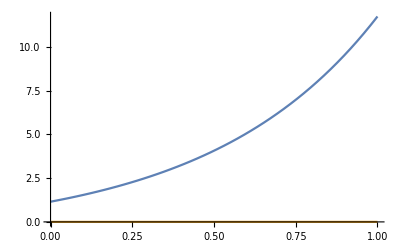

```mathematica
V02smooth[μ_]:=((2-4 μ^2)(1-ⅇ^(2 μ  ϕcyc) Cos[ϕcyc])+6μ ⅇ^(2 μ  ϕcyc)  Sin[ϕcyc])/(1+4 μ^2);
V02smooth[μ]
FullSimplify[V02smooth[0]]
(4/π)Sin[ϕcyc]
N[V02smooth[0]]
Plot[{V02smooth[μ],0},{μ,0,1}]
```

### Cycloid

```mathematica
Solve[v2cyc[π/2,μ,V02]==0,V02][[1]][[1]]
```

V02→(4 (ⅇ^(π μ)-μ^2))/(1+μ^2)

4.

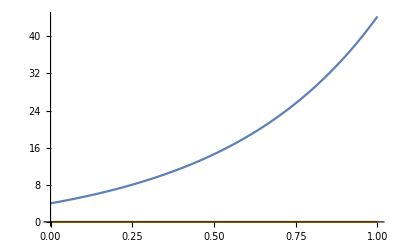

```mathematica
V02smoothcyc[μ_]:=(4 (ⅇ^(π μ)-μ^2))/(1+μ^2)
N[V02smoothcyc[0]]
Plot[{V02smoothcyc[μ],0},{μ,0,1}]
```

## Energy loss

The expression for the energy loss is
ΔE=-∫frⅆs=μ∫_0^s Nⅆs=μ∫_0^φ N(φ)(ⅆφ/κ(φ))

and since N(φ)=mg cos(φ)+m v^2(φ)κ(φ), we have
ΔE=μ∫_0^φ [mg cos(φ)+m v^2(φ)κ(φ)](ⅆφ/κ(φ)) =μm∫_0^φ [g cos(φ)/κ(φ)+ v^2(φ)]ⅆφ

### Energy loss climbing the circle

From the equation above and a curvature for the circle of κ(φ)=1/R
ΔE=μm∫_0^φ [g R cos(φ)+ v^2(φ)]ⅆφ  

Normalizing the energy by gR we have
ΔE/gR=μm∫_0^φ [cos(φ)+ v^2(φ)/gR]ⅆφ  

The two terms are:

```mathematica
FullSimplify[∫_0^ϕ (V02 Exp[-2 μ p]+ g A ((2-4 μ^2)(Cos[p]-Exp[-2 μ p])-6μ Sin[p])/(1+4 μ^2))ⅆp]
```

-((-1+ⅇ^(-2 μ ϕ)) V02)/(2 μ)+(A g (6 μ (-1+Cos[ϕ])+(2-4 μ^2) ((-1+ⅇ^(-2 μ ϕ))/(2 μ)+Sin[ϕ])))/(1+4 μ^2)

Remember that v2circ = v^2(φ)/gR is already normalized (dimensionless):

```mathematica
FullSimplify[∫_0^ϕ v2circ[ϕ,μ,V02]ⅆϕ]
```

-((-1+ⅇ^(-2 μ ϕ)) V02)/(2 μ)+(6 μ (-1+Cos[ϕ])+(2-4 μ^2) ((-1+ⅇ^(-2 μ ϕ))/(2 μ)+Sin[ϕ]))/(1+4 μ^2)

```mathematica
FullSimplify[∫_0^ϕ (g A Cos[p])ⅆp]
```

A g Sin[ϕ]

Therefore, the dimensionless energy change can be expressed by
ΔE/(mgR)=μ∫_0^φ [cos(φ)+ v^2(φ)/gR]ⅆφ 
                            =  μ(sin(φ) + -((-1+ⅇ^(-2 μ ϕ)) V02)/(2 μ)+(6 μ (-1+Cos[ϕ])+(2-4 μ^2) ((-1+ⅇ^(-2 μ ϕ))/(2 μ)+Sin[ϕ]))/(1+4 μ^2))

```mathematica
Ecirc[ϕ_,μ_,V02_]:= μ(Sin[ϕ] + -((-1+ⅇ^(-2 μ ϕ)) V02)/(2 μ)+(6 μ (-1+Cos[ϕ])+(2-4 μ^2) ((-1+ⅇ^(-2 μ ϕ))/(2 μ)+Sin[ϕ]))/(1+4 μ^2))
```

```mathematica
Ecirc[Pi/8,0.01,10]
```

0.0427278

Now, we can evaluate v2circ and Ecirc only up to the point were the velocity becomes zero. It does not make sense to evaluate either v2circ or the energy beyond this point:

```mathematica
ϕstop[μ_,V02_]:=ϕ/.FindRoot[v2circ[ϕ,μ,V02],{ϕ,0,Pi/2}]
ϕstop[0.5,2]
```

0.774381

```mathematica
Manipulate[Plot[{v2circ[p,mu,v02],v2circ[ϕcyc,mu,v02]},{p,0,Pi/2},PlotRange->{{0,Pi/2},{0,5}},AxesLabel->{"ϕ","V0^2(ϕ)/gA"},Ticks->{{{0,"0"},{Pi/8,"π/8"},{Pi/4,"π/4"},{ϕcyc,"ϕcyc"},{Pi/2,"π/2"}},Automatic}],{mu,0,2},{v02,2,5}]

Manipulate[Plot[{Ecirc[ϕ,μ,V02],Piecewise[{{Ecirc[ϕ,μ,V02],ϕ>ϕstop[μ,V02]}}]},{ϕ,0,ϕcyc},PlotRange->{{0,π/2},{0,3}},AxesLabel->{"ϕ","ΔE_cir/(mgR)"},Epilog->{Text["Allowed values",{ϕstop[μ,V02]/2,1},{0,-1}]},Ticks->{{{0,"0"},{Pi/8,"π/8"},{Pi/4,"π/4"},{ϕcyc,"ϕcyc"},{Pi/2,"π/2"}},Automatic},Filling->{2->{1}}],{μ,0.01,2},{V02,0,5},Initialization:>(μ=0.5;V02=1)]
```

Plot::plln: Limiting value ϕcyc in {ϕ,0,ϕcyc} is not a machine-sized real number.

### Energy loss in the cycloid

From the equation above and a curvature for the cycloid of κ(φ)=sec(φ)/4B,
ΔE=μm∫_0^φ [g  cos(φ) (4B cos(φ))+ v^2(φ)]ⅆφ  

Normalizing the energy by gB we have
ΔE/gB=μm∫_0^φ [4 cos^2(φ)+ v^2(φ)/gR]ⅆφ  

The two terms are:

```mathematica
FullSimplify[∫_0^ϕ (V02 Exp[-2 μ p]- g B (4(Sin[p]+μ Cos[p])^2-4 μ^2 Exp[-2 μ p])/(1+μ^2))ⅆp]
```

-((-1+ⅇ^(-2 μ ϕ)) V02)/(2 μ)-(B g (2 (ϕ+μ (ⅇ^(-2 μ ϕ)+μ ϕ))-2 μ Cos[2 ϕ]+(-1+μ^2) Sin[2 ϕ]))/(1+μ^2)

```mathematica
FullSimplify[∫_0^ϕ (v2cyc[ϕ,μ,V02]-V02 Exp[-2 μ ϕ])ⅆϕ ]
```

-(2 (ϕ+μ (ⅇ^(-2 μ ϕ)+μ ϕ))-2 μ Cos[2 ϕ]+(-1+μ^2) Sin[2 ϕ])/(1+μ^2)

```mathematica
FullSimplify[∫_0^ϕ V02 Exp[-2 μ ϕ]ⅆϕ]
```

-((-1+ⅇ^(-2 μ ϕ)) V02)/(2 μ)

```mathematica
FullSimplify[∫_0^ϕ (g  Cos[p])(4 B Cos[p])ⅆp]
```

B g (2 ϕ+Sin[2 ϕ])

Therefore, the dimensionless energy change can be expressed by
ΔE/(mgB)=μ∫_0^ϕ [4 cos^2(φ)+ v^2(φ)/gR]ⅆφ
                            =   μ(2ϕ+sin(2ϕ) +((1-ⅇ^(-2 μ ϕ)) V02)/(2 μ)-(2 (ϕ+μ (ⅇ^(-2 μ ϕ)+μ ϕ))-2 μ Cos[2 ϕ]+(-1+μ^2) Sin[2 ϕ])/(1+μ^2))

```mathematica
Ecyc[ϕ_,μ_,V02_]:=μ(2ϕ+Sin[2ϕ]+((1-ⅇ^(-2 μ ϕ)) V02)/(2 μ)-(2 (ϕ+μ (ⅇ^(-2 μ ϕ)+μ ϕ))-2 μ Cos[2 ϕ]+(-1+μ^2) Sin[2 ϕ])/(1+μ^2))
Ecyc[Pi/8,0.01,10]
```

0.0531998

Now, we can evaluate v2cyc only up to the point were the velocity becomes zero. It does not make sense to evaluate either v2cyc or the energy beyond this point:

```mathematica
ϕstopcyc[μ_,V02_]:=ϕ/.FindRoot[v2cyc[ϕ,μ,V02],{ϕ,0,Pi/2}]
ϕstopcyc[0.5,2]
```

0.326674

```mathematica
Manipulate[Plot[v2cyc[p,mu,v02],{p,0,Pi/2},PlotRange->{{0,Pi/2},{0,5}},AxesLabel->{"ϕ","V0^2(ϕ)/gA"},Ticks->{{{0,"0"},{Pi/8,"π/8"},{Pi/4,"π/4"},{Pi/2,"π/2"}},Automatic}],{mu,0,1},{v02,0,5},Initialization:>(mu=0.5;v02=1)]

Manipulate[Plot[{Ecyc[ϕ,μ,V02],Piecewise[{{Ecyc[ϕ,μ,V02],ϕ>ϕstopcyc[μ,V02]}}]},{ϕ,0,π/2},PlotRange->{{0,π/2},{0,10}},AxesLabel->{"ϕ","ΔE_cyc/(mgR)"},Epilog->{Text["Allowed values",{ϕstopcyc[μ,V02]/2,1},{0,-1}]},Ticks->{{{0,"0"},{Pi/8,"π/8"},{Pi/4,"π/4"},{ϕcyc,"ϕcyc"},{Pi/2,"π/2"}},Automatic},Filling->{2->{1}}],{μ,0.01,1},{V02,0,15},Initialization:>(μ=0.5;V02=1)]
```

### Energy loss: combined circle and cycloid

```mathematica
Manipulate[Plot[{v2circ[p,mu,v02],v2circ[ϕcyc,mu,v02],v2cyc[p,mu,v02cyc]},{p,0,Pi/2},PlotRange->{{0,Pi/2},{0,10}},PlotLegends->{"Circle",None,"Cycloid"},AxesLabel->{"ϕ","V0^2(ϕ)/gA"},Ticks->{{{0,"0"},{Pi/8,"π/8"},{Pi/4,"π/4"},{ϕcyc,"ϕcyc"},{Pi/2,"π/2"}},Automatic}],{mu,0,1},{v02,0,10},{v02cyc,0,10},Initialization:>(mu=0.1;v02=2;v02cyc=2)]

Manipulate[Plot[{Ecirc[ϕ,μ,V02],Piecewise[{{Ecirc[ϕ,μ,V02],ϕ>ϕstop[μ,V02]}}],Ecyc[ϕ,μ,V02cyc],Piecewise[{{Ecyc[ϕ,μ,V02cyc],ϕ>ϕstopcyc[μ,V02cyc]}}]},{ϕ,0,Pi/2},PlotRange->{{0,π/2},{0,3}},AxesLabel->{"ϕ","ΔE/(mgR)"},PlotLegends->{"Circle",None,"Cycloid",None},Epilog->{Text["Allowed values",{ϕstop[μ,V02]/2,1},{0,-1}]},Ticks->{{{0,"0"},{Pi/8,"π/8"},{Pi/4,"π/4"},{ϕcyc,"ϕcyc"},{Pi/2,"π/2"}},Automatic},Filling->{1->{2},3->{4}}],{μ,0.01,1},{V02,0,10},{V02cyc,0,10},Initialization:>(μ=0.5;V02=2;V02cyc=2)]
```

### Energy loss circle with terminal velocity zero

Let’s explore how the energy loss increases until the particle stops:

```mathematica
Manipulate[Plot[{Ecirc[ϕ,μ,V02],v2circ[ϕ,μ,V02]},{ϕ,0,ϕstop[μ,V02]},PlotLegends->{"∆E circ","V02 circ"},Ticks->{{{0,"0"},{Pi/8,"π/8"},{Pi/4,"π/4"},{ϕcyc,"ϕcyc"},{Pi/2,"π/2"}},Automatic},PlotRange->{{0,π/2},{0,3}}],{μ,0.01,1},{V02,0.01,10}]
```

Plot::plln: Limiting value ϕstop[0.294,2.6] in {ϕ,0,ϕstop[0.294,2.6]} is not a machine-sized real number.

With the exact initial velocity  needed to get with zero velocity to the cusp, we can explore the different energies:

```mathematica
Kin[ϕ_,μ_,V02_]:=v2circ[ϕ,μ,V02smooth[μ]]/2
Pot[ϕ_,μ_,V02_]:=1-Cos[ϕ]
Manipulate[Plot[{Ecirc[ϕ,μ,V02smooth[μ]],Kin[ϕ,μ,V02smooth[μ]],Pot[ϕ,μ,V02smooth[μ]],Kin[ϕ,μ,V02smooth[μ]]+Pot[ϕ,μ,V02smooth[μ]],1.01Kin[0,μ,V02smooth[μ]]-(Kin[ϕ,μ,V02smooth[μ]]+Pot[ϕ,μ,V02smooth[μ]]),v2circ[ϕ,μ,V02smooth[μ]]},{ϕ,0,ϕstop[μ,V02smooth[μ]]},PlotLegends->{"∆E","K","U","K+U","E0-(K+U)","V2"},Ticks->{{{0,"0"},{Pi/8,"π/8"},{Pi/4,"π/4"},{ϕcyc,"ϕcyc"},{Pi/2,"π/2"}},Automatic},PlotRange->{{0,π/2},{0,3}}],{μ,0.01,1}]
```

Plot::plln: Limiting value ϕstop[0.17,V02smooth[0.17]] in {ϕ,0,ϕstop[0.17,V02smooth[0.17]]} is not a machine-sized real number.

In the paper by Reyes-Portales et al, they just study two particular cases: μ=0.5 and μ=0.8. They report the following initial velocities (and I agree):

```mathematica
Sqrt[V02smooth[0.5]*g*A]
Sqrt[V02smoothcyc[0.5]*g*B]

Sqrt[V02smooth[0.8]*g*A]
Sqrt[V02smoothcyc[0.8]*g*B]
```

8.31131

8.45626

11.4724

11.8276

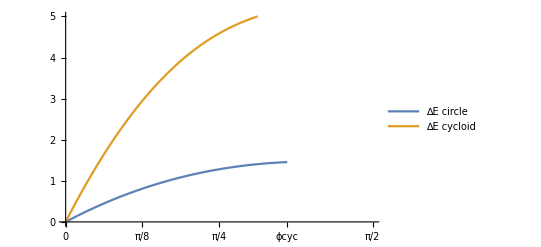

-Graphics-

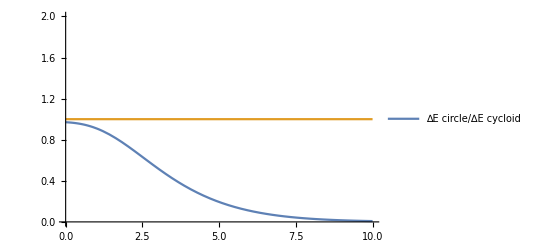

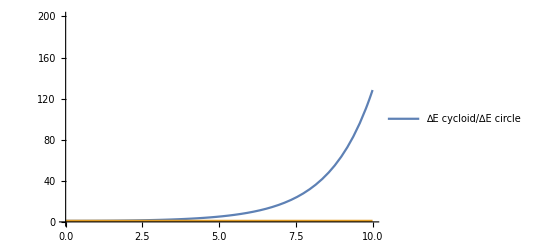

Plot::plln: Limiting value ϕstop[0.511,V02smooth[0.511]] in {ϕ,0,ϕstop[0.511,V02smooth[0.511]]} is not a machine-sized real number.

```mathematica
plotEnergies[μ_]:=Plot[{Ecirc[ϕ,μ,V02smooth[μ]],Ecyc[ϕ,μ,V02smoothcyc[μ]]},{ϕ,0,ϕstop[μ,V02smooth[μ]]},PlotLegends->{"∆E circle","∆E cycloid"},Ticks->{{{0,"0"},{Pi/8,"π/8"},{Pi/4,"π/4"},{ϕcyc,"ϕcyc"},{Pi/2,"π/2"}},Automatic},PlotRange->{{0,π/2},{0,5}}];

plotEnergies[0.5]

Plot[{g*A*Ecirc[ϕcyc,μ,V02smooth[μ]],g*B*Ecyc[π/2,μ,V02smoothcyc[μ]]},{μ,0,1},PlotLegends->{"∆E circle (in J)","∆E cycloid (in J)"},AxesLabel->{"μ"}]

Manipulate[Plot[{ (π/(2 Sin[ϕcyc]))Ecirc[ϕ,μ,V02smooth[μ]],(1/2)Ecyc[ϕ,μ,V02smoothcyc[μ]]},{ϕ,0,ϕstop[μ,V02smooth[μ]]},PlotLegends->{"∆E circle","∆E cycloid"},Ticks->{{{0,"0"},{Pi/8,"π/8"},{Pi/4,"π/4"},{ϕcyc,"ϕcyc"},{Pi/2,"π/2"}},Automatic},PlotRange->{{0,π/2},{0,5}}],{μ,0.01,1}]

Plot[{ (π/(2 Sin[ϕcyc]))Ecirc[ϕcyc,μ,V02smooth[μ]]/((1/2)Ecyc[π/2,μ,V02smoothcyc[μ]]),1},{μ,0,10},PlotLegends->{"∆E circle/∆E cycloid"},PlotRange->{{0,10},{0,2}}]
Plot[{ ((1/2)Ecyc[π/2,μ,V02smoothcyc[μ]])/((π/(2 Sin[ϕcyc]))Ecirc[ϕcyc,μ,V02smooth[μ]]),1},{μ,0,10},PlotLegends->{"∆E cycloid/∆E circle"},PlotRange->{{0,10},{0,200}}]
```

This is interesting (above): For friction coefficients μ >1, the energy dissipated in the circular track is not only smaller  than the energy dissipated on the cycloid; but it tends to zero!!! For really large friction, the energy dissipated on the cycloid is way larger than in the circle, even if it takes less time to get there.

```mathematica
Ecirc[ϕcyc,μsol,V02smooth[μsol]]
Ecirc[ϕcyc,0.5,V02smooth[0.5]]
```

0.576801

1.45607

```mathematica
g*A*Ecirc[ϕcyc,0.5,V02smooth[0.5]]
g*B*Ecyc[Pi/2,0.5,V02smoothcyc[0.5]]
```

24.7389

25.9541

```mathematica
g*A*Ecirc[ϕcyc,0.8,V02smooth[0.8]]
g*B*Ecyc[Pi/2,0.8,V02smoothcyc[0.8]]
```

56.0084

60.1462

```mathematica
g*A*Ecirc[ϕcyc,1,V02smooth[1]]
g*B*Ecyc[Pi/2,1,V02smoothcyc[1]]
```

89.8802

98.6894

#### Special μ: ∆E = E(ϕcyc)=U(ϕcyc)

There is only one friction coefficient that satisfies simultaneously that
1) The particle gets to ϕcyc with zero velocity
2) The dissipated energy is equal to the total mechanical energy (gravitational energy).

```mathematica
Pot[ϕcyc,μ,V02smooth[μ]]
FullSimplify[Ecirc[ϕcyc,μ,V02smooth[μ]]]
```

1-√(1-(16 π^2)/((4+π^2)^2))

(-4+π^2-2 (20+π^2) μ^2+ⅇ^(2 μ ArcSin[(4 π)/(4+π^2)]) (4-π^2+12 π μ+2 (-4+π^2) μ^2))/((4+π^2) (1+4 μ^2))

Solving Ecirc[ϕcyc,μ,V02smooth[μ]]==Pot[ϕcyc,μ,V02smooth[μ]]

(-12+π^2-2 (36+π^2) μ^2+ⅇ^(2 μ ArcSin[(4 π)/(4+π^2)]) (4-π^2+12 π μ+2 (-4+π^2) μ^2))/(1+4 μ^2)==0

{μ→0.256215}

0.256215

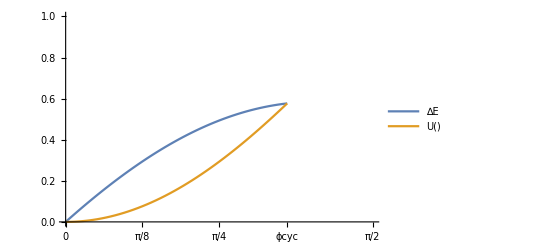

0.576801

0.576801

```mathematica
FullSimplify[Ecirc[ϕcyc,μ,V02smooth[μ]]-Pot[ϕcyc,μ,V02smooth[μ]]==0]
FindRoot[Ecirc[ϕcyc,μ,V02smooth[μ]]-Pot[ϕcyc,μ,V02smooth[μ]],{μ,0.01,1}]
μsol=μ /.FindRoot[Ecirc[ϕcyc,μ,V02smooth[μ]]-Pot[ϕcyc,μ,V02smooth[μ]],{μ,0.01,1}]

Plot[{Ecirc[ϕ,μsol,V02smooth[μsol]],Pot[ϕ,μsol,V02smooth[μsol]]},{ϕ,0,ϕcyc},PlotLegends->{"∆E","U()"},Ticks->{{{0,"0"},{Pi/8,"π/8"},{Pi/4,"π/4"},{ϕcyc,"ϕcyc"},{Pi/2,"π/2"}},Automatic},PlotRange->{{0,π/2},{0,1}}]
Ecirc[ϕcyc,μsol,V02smooth[μsol]]
N[Pot[ϕcyc,μsol,V02smooth[μsol]]]
```

### Some thoughts about this special ∆E = E(ϕcyc)=U(ϕcyc)

If we think of the frictionless case, conservation of energy tells that


Dividing by  and remembering that   we get that the initial speed must be


as we get from our general expression:

```mathematica
Simplify[V02smooth[0]]
```

16/(4+π^2)

When  increases, the initial velocity must be higher in order to reach the cusp. However the final potential energy will still be

which is the same as the original, total energy of the system without friction. The energy dissipated will increase more as the coefficient of friction increases, but it can be smaller or higher than the final potential energy. The boundary is set by the equation



which means that

```mathematica
Simplify[Pot[ϕcyc,μ,V02smooth[μ]]]
```

8/(4+π^2)

But in addition, we know that the energy dissipated is always the difference between the initial and final total mechanical energy:


where  = V02smooth[μ].  So, in the particular case with this energy dissipated is equal to the potential energy, we have

which implies that we have to launch the particle with twice the velocity we needed when there was no friction:


In normalized-velocity terms, 


which is equal to


and also equal to

```mathematica
V02smooth[μsol]
```

2.3072

```mathematica
N[2*16/(4+π^2)]
```

2.3072

```mathematica
N[8 Sin[ϕcyc]/π]
```

2.3072

```mathematica
Simplify[2V02smooth[0]]
N[2V02smooth[0]]
```

32/(4+π^2)

2.3072

Any friction coefficient higher than this μ=μsol = 0.256215 will result in a dissipation of energy that is higher than the final potential energy. Rather than obtaining this special friction coefficient from , I could obtain it from the equation above, since I know the speed. Basically, μsol  satisfies V02smooth[μsol]=32/(4+π^2):

```mathematica
Simplify[V02smooth[μ](1+4μ^2)==32/(4+π^2)(1+4μ^2)]
```

π^2+ⅇ^(2 μ ArcSin[(4 π)/(4+π^2)]) (4+12 π μ-8 μ^2+π^2 (-1+2 μ^2))==2 (6+(36+π^2) μ^2)

```mathematica
FindRoot[π^2+ⅇ^(2 μ ArcSin[(4 π)/(4+π^2)]) (4+12 π μ-8 μ^2+π^2 (-1+2 μ^2))-2 (6+(36+π^2) μ^2),{μ,0.1,1}]
```

{μ→0.256215}

## Phase diagrams

The energy that has been dissipated by the time the particle gets to the top of the cusp is given by Ecircle[ϕcyc,μ,V02] and Ecyc[π/2,μ,V02]. The possible values of Ecyc at this location are shown in the contour plot below.

Note that in only one case the particle gets to the cusp () with zero velocity: if it is starts with an initial velocity of V02smooth[μ]:

```mathematica
FullSimplify[V02smooth[μ]]
```

(2-4 μ^2+(2 ⅇ^(2 μ ArcSin[(4 π)/(4+π^2)]) (4-π^2+12 π μ+2 (-4+π^2) μ^2))/(4+π^2))/(1+4 μ^2)

ArcSin[(4 π)/(4+π^2)]

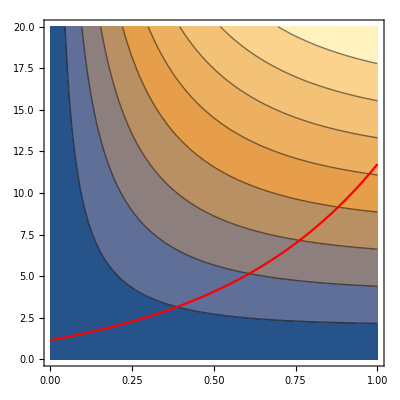

```mathematica
ϕcyc
Show[ContourPlot[Ecirc[ϕcyc,μ,V02],{μ,0.001,1},{V02,0,20}],Plot[V02smooth[x],{x,0,1},PlotStyle->Red]]
```

For the cycloid, we had

```mathematica
V02smoothcyc[μ]
N[V02smoothcyc[0]]
```

(4 (ⅇ^(π μ)-μ^2))/(1+μ^2)

4.

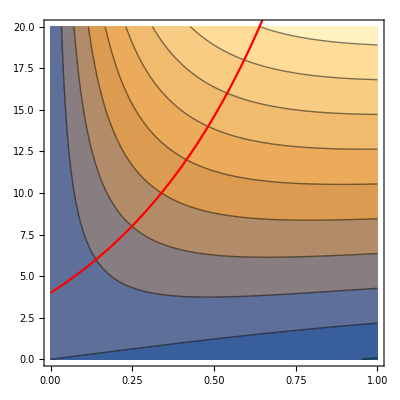

```mathematica
Show[ContourPlot[ Ecyc[π/2,μ,V02],{μ,0,1},{V02,0,20}],Plot[V02smoothcyc[x],{x,0,1},PlotStyle->Red]]
```

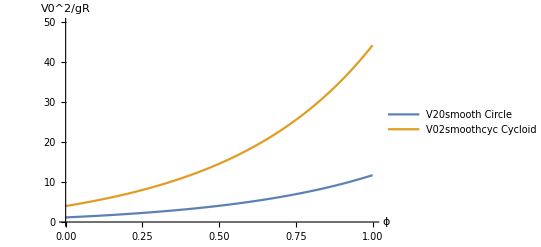

```mathematica
Plot[{V02smooth[μ],V02smoothcyc[μ]},{μ,0,1},PlotLegends->{"V20smooth Circle","V02smoothcyc Cycloid"},PlotRange->{{0,1},{0,50}},AxesLabel->{"ϕ","V0^2/gR"}]
```

```mathematica
Clear[A,B]
A=((2 π^2)/(4+π^2))
B=1/2;
Plot[{9.8A Ecirc[ϕcyc,μ,V02smooth[μ]],9.8B Ecyc[Pi/2,μ,V02smoothcyc[μ]]},{μ,0,1},PlotRange->{0,100},PlotLegends->{"Circle","Cycloid"}]
N[ 9.8*A*Ecirc[ϕcyc,1,V02smooth[1]]]
N[ 9.8 *B*Ecyc[Pi/2,1,V02smoothcyc[1]]]
```

(2 π^2)/(4+π^2)

-Graphics-

13.9474 Ecirc[1.13382,1.,11.7338]

4.9 Ecyc[1.5708,1.,V02smoothcyc[1.]]

## Animations

Since v(t)=dr/dt=(dr/dφ)(dφ/dt),    then  |v(t)|= |dr/dφ||dφ/dt|=R|dφ/dt| implies that
 dφ/dt = Sqrt[(v(t))^2]/R

```mathematica
g=9.8;
R=1.0;
Clear[φ];
A=(π/2)/((4π)/(4+π^2));
B=0.5;
μ0=0.5;
v0circle=5;
v0cycloid=10;
sol=NDSolve[{y'[t]==Abs[Sqrt[v2circ[y[t],μ0,V02smooth[μ0]](g A)]]/A,y[0]==0},y,{t,0,15}];
solcyc=NDSolve[{y2'[t]==Abs[Sqrt[v2cyc[y2[t],μ0,V02smoothcyc[μ0]](g B)]]/B,y2[0]==0},y2,{t,0,15}];
φ[t_]:=Evaluate[y[t]/.sol][[1]]
φcycloid[t_]:=Evaluate[y2[t]/.solcyc][[1]]
rcircle[t_]:=A{Sin[φ[t]],1-Cos[φ[t]]}
rcycloid[t_]:=B{2φcycloid[t]+Sin[2φcycloid[t]],1-Cos[2φcycloid[t]]}

Animate[Show[ParametricPlot[{rcircle[t],rcycloid[t]},{t,0,1},PlotRange->{0,3B},PlotLegends->{"Circle","Cycloid"}],Graphics[{Red,Disk[rcircle[T],0.04]}],Graphics[{Blue,Disk[rcycloid[T],0.04]}]],{T,0,0.5}]
```

## Timings

We our parameterizations,



we are looking for the time it takes to travel up to the angle :


Since      then  |v(t)|= |dr/dφ||dφ/dt|.
For the circle, |dr/dφ| = R                    ---> |dφ/dt| = |v(t)|/R
For the cycloid, |dr/dφ| = 4B cosφ  ---> |dφ/dt| = |v(t)|/(4B cosφ(t) )
 
 Therefore, for the circle we have
 dφ/dt = |v(t)|/R = Sqrt[gR*((v(t))^2/gR)]/R
 
 and for the cycloid,
 dφ/dt =   |v(t)|/(4B cosφ(t) ) = Sqrt[gB ((v(t))^2/gB)]/( 4B cosφ )

1/8 (4+π^2)

0.709613

4

4 Cos[ϕp]^2

0.451754 Abs[Cos[ϕp]] Sec[ϕp]

0.709613

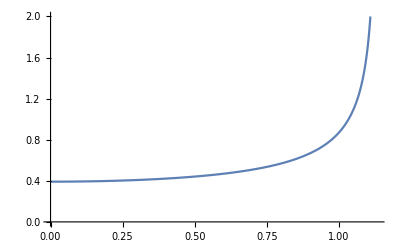

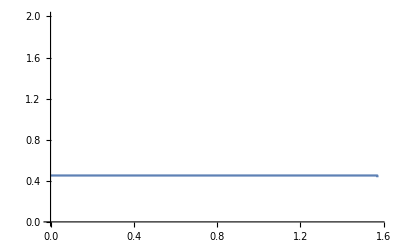

-Graphics-

-Graphics-

```mathematica
g=9.8;
A=(π/2)/((4π)/(4+π^2));
A
B=0.5;
tcirc[ϕ_,μ_,V02_]:=NIntegrate[A/Sqrt[g A  v2circ[ϕp,μ,V02]],{ϕp,0,ϕ}]
tcyc[ϕ_,μ_,V02_]:=NIntegrate[4 B Cos[ϕp]/Sqrt[g B v2cyc[ϕp,μ,V02]],{ϕp,0,ϕ}]


∫_0^(Pi/2) 4 B Cos[ϕp]/Sqrt[g B v2cyc[ϕp,0,V02smoothcyc[0]]]ⅆϕp
V02smoothcyc[0]
FullSimplify[v2cyc[ϕp,0,V02smoothcyc[0]],ϕp>0]
FullSimplify[4 B Cos[ϕp]/Sqrt[g B v2cyc[ϕp,0,V02smoothcyc[0]]],ϕp>0]
Sqrt[ B/g]Pi

Plot[A/Sqrt[g A v2circ[ϕp,0,V02smooth[0]]],{ϕp,0,ϕcyc},PlotRange->{0,2}]
Plot[4 B Cos[ϕp]/Sqrt[g B v2cyc[ϕp,0,V02smoothcyc[0]]],{ϕp,0,Pi/2},PlotRange->{0,2}]

Manipulate[Plot[{tcirc[ϕ,μ,V02smooth[μ]],tcyc[ϕ,μ,V02smoothcyc[μ]],tcyc[π/2,μ,V02smoothcyc[μ]]},{ϕ,0,Pi/2},PlotLegends->{"t circle","t cycloid"},Ticks->{{{0,"0"},{Pi/8,"π/8"},{Pi/4,"π/4"},{ϕcyc,"ϕcyc"},{Pi/2,"π/2"}},Automatic},PlotRange->{{0,π/2},{0,0.72}},AxesLabel->{"ϕ","Time (s)"}],{μ,0,10}]

Plot[{tcirc[ϕcyc,μ,V02smooth[μ]],tcyc[Pi/2,μ,V02smoothcyc[μ]]},{μ,0,100},PlotRange->{{0,100},{0,1}},AxesLabel->{"μ","Time (s)"},PlotLabels->{"Circle","Cycloid"}]
Plot[(tcirc[ϕcyc,μ,V02smooth[μ]]-tcyc[Pi/2,μ,V02smoothcyc[μ]]),{μ,0,100},PlotRange->{{0,100},{0,.05}},AxesLabel->{"μ","Time (s)"},PlotLabels->{"Circle-Cycloid"}]
```

There is a maximum!  And actually, the time difference is smaller at larger friction!

```mathematica
timediff[μ_]:=tcirc[ϕcyc,μ,V02smooth[μ]]-tcyc[Pi/2,μ,V02smoothcyc[μ]]
timediff[0]
timediff[100]
timediff[150]
```

0.00842882

0.00293308

0.00198312